/Users/prentner/agent based modeling/Perceptual_networks_clean/perceptual network

*** | perceptual network/states/2020_0914_2030.csv |  |  |  | 
*** | numagents | n_pop | n_ind | graph_density | adjacency
16 | 0 | 0 | 0.233333 |  |

edges: {1<->3,1<->4,1<->5,1<->6,1<->8,1<->9,1<->10,1<->16,2<->3,2<->4,2<->5,2<->6,2<->7,3<->14,4<->13,5<->8,5<->9,5<->10,5<->15,6<->7,6<->15,7<->11,7<->12,9<->11,9<->12,9<->16,10<->13,12<->14}

Degree Centrality:3.5

Edge density: 0.233333

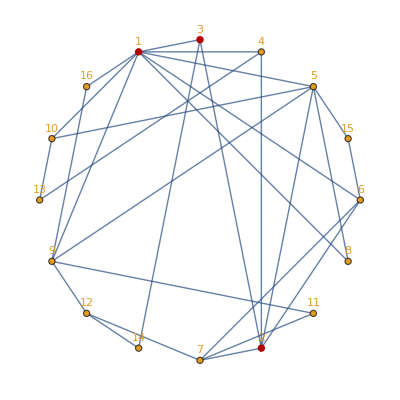

figures/fig1.pdf

```mathematica
(* import csv file from simulation; NOTE: change indexing from 0->1 *)
SetDirectory[NotebookDirectory[]]
data=Import["states/2020_0914_2030.csv"] ;
data[[1;;3]]//TableForm (* preview first 20 rows of file *)
(* load input parameters *)
i=1;
While[ data[[i,1]]=="***" ;i++]
i++;
numagents = data[[i,1]];
npop = data[[i,2]];
nind = data[[i,3]];
density = data[[i,4]];
i++;
(* read adjacency *)
start = i;
end = start + numagents -1;
adj = data[[start;;end,1]];
adjacency=ToExpression[StringSplit[adj,{" ", "[", "]"}]];
adjacency//TableForm;
i=end+1;
(* create edge list from adjacency *)
edraw0={};
Do[
	Do[
		If[adjacency[[ia1,ia2]]==1,{edraw0=Append[edraw0,ia1<-> ia2]}]		
	,{ia2,ia1+1,numagents}]
,{ia1,1,numagents}]
Print["edges: ", edraw0]
Print["Degree Centrality:", Mean[DegreeCentrality[g]]//N]
Print["Edge density: ", N[2*Length[edraw0]/(numagents^2-numagents)]]
(* draw graph *)
g= Graph[edraw0,VertexLabels->Placed["Name",Above],DirectedEdges->False,VertexSize->0.1,VertexStyle->ColorData[97,"ColorList"][[2]]
,GraphLayout->"CircularEmbedding"];
HighlightGraph[g,{1,2,3}]
Export["figures/fig1.pdf",g]
```

{0,1,1,1,4,3,4,5,3,3,6,4,1,4,2,2,2,2,3,4,4,3,6,5,5,3,6,4,3,4,3,2,2,3,2.94 2.2,3.75 1.53,0.}

{maj,0,4,3,2,2,3,2,2,1,3,2,1,2,1,1,1,1,8,5,3,3,6,4,4,2,5,3,2,3,2,2,2,2,1.94 0.86,3.5  3.07,0.552}

{mxt,0,8,5,3,3,6,4,4,2,5,3,2,3,2,2,2,2,8,5,3,3,6,4,4,2,5,3,2,3,2,2,2,2,3.5  3.07,3.5  3.07,0.}

Populations: 50 Individuals: 24

Transpose::tperm: Permutation {9,5,2,3,3,2,2,2,2,2,2,5,3,1,1,3} is longer than the dimensions {16} of the expression.

Transpose[{6,1,1,1,1,1,1,2,2,1,2,4,1,1,1,3},{9,5,2,3,3,2,2,2,2,2,2,5,3,1,1,3}]

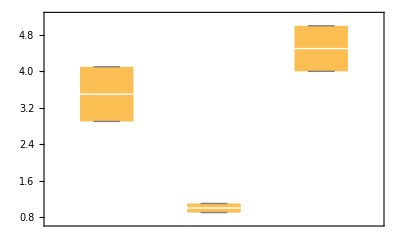

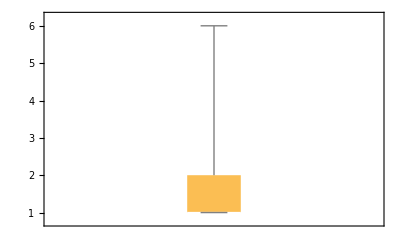

```mathematica
(* read thresholds per pop *)
While[ data[[i,1]]=="***" ;i++]
data[[i]]
e=i;
While[ IntegerQ[data[[e,1]]],e++]
data[[e]]
e++;
data[[e]]
npop= data[[e-2,1]];
nind = data[[e-2,2]];
Print["Populations: ", npop, " Individuals: ", nind]
thresh = ReverseSortBy[data[[e-2-nind;;e-2]],Last];
Transpose[thresh[[1,3;;numagents+2]],thresh[[1,3+numagents;;2*numagents+2]]]
mu = {{2.9,4.1},{0.9,1.1},{4,5} };
BoxWhiskerChart[mu]
mu1 = BoxWhiskerChart[ thresh[[1,3;;numagents+2]]];(* , InterpolationOrder->0,Mesh->All,Filling->Axis,FillingStyle->White]*); (*μ_1 *)
mu2 = ListPlot[ thresh[[1,numagents+3;;2*numagents+2]] , InterpolationOrder->0,Joined->False,Mesh->All,Filling->Axis]; (*μ_2 *)
Show[mu1,PlotRange->All,Frame->True]
```

{1,2,3}

{4,5,6,7,8,9,10,11,12,13,14,15,16}

{{4,5,8,11,13},{6,10,12,14,16},{7,9,15}}

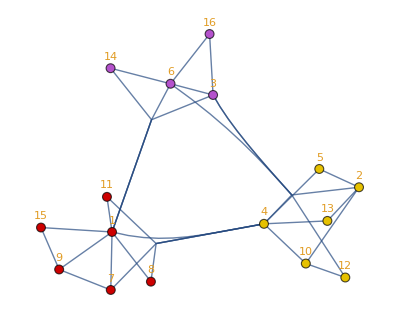

figures/fig1_community.pdf

```mathematica
(* find and plot graph communities *)
sizeinput = 3;
inodes = Table[i,{i,1,sizeinput}]
remainder = Table[i,{i,sizeinput+1,numagents}]
communities = FindGraphCommunities[cg,Method->"Modularity"]
cg=CommunityGraphPlot[g,CommunityBoundaryStyle->None,VertexSize->0.25]
Export["figures/fig1_community.pdf",cg]
```